```mathematica
Question 1
```

In the following explanations:
w_t - wages at time t
r_t - return on capital at time t
C_t - consumption at time t
L_t - labour at time t
K_t- capital at time t
I_t - investment at time t
Y_t  - output at time t
(K^f)_t - firms choice of capital at time t
(L^f)_t - firms choice of labour at time t
Π_t - profits at time t
(Π^f)_t - firm profits at time t
δ - depreciation of capital
A - level of technology
α - Capital income share

### Part A

A competitive equilibrium consists of:  a set of prices  {w_t, r_t}(_(t=0))^∞ ;  allocations for the household {C_t, L_t, K_t, I_t}(_(t=0))^∞ ; allocations for the firm {(K^f)_t, (L^f)_t}(_(t=0))^∞ ;  household and firm profits  {Π_t, (Π^f)_t}(_(t=0))^∞ such that:

1. Given the set of prices, {w_t, r_t}(^∞)_(t=0) and allocations of the representative household, {C_t, L_t, K_t, L_t}(^∞)_(t=0) , solves the household problem given by:

Maximise ∑_(t=0)^∞ β^t log(C_t) 

with respect to {C_t, K_(t+1), L_t}(^∞)_(t=0)

subject to:

 C_t + I_t = w_t L_t + r_t K_t + Π_t, ∀t
 K_(t+1) = (1 - δ)  K_t +  I_t,  ∀t
 L_t  =  1, ∀t
 K_0 = K^- (given)
 
 2. Given the set of prices, {w_t, r_t}(^∞)_(t=0) and allocations of the representative firm, {(K^f)_t, (L^f)_t}(^∞)_(t=0),  solves the firm problem given by:
 
Maximise  (Π^f)_t = Y_t - w_t(L^f)_t - r_t(K^f)_t,  where  Y_t =  ((K^f)_t)^α  (A(L^f)_t)^(1-α) ,  ∀t

with respect to {(K^f)_t, (L^f)_t},  ∀t

3. Markets clear:

Y_t =  C_t + I_t, , ∀t (Goods market)
(L^f)_t= L_t = 1, , ∀t (Labour Market)
(K^f)_t = K_t , ∀t (Capital Markets)

4. Firm profits equal household profits:

(Π^f)_t = Π_t (which given the Model’s perfect competition both equal 0)

Part B

To achieve the competitive equilibrium we must find the model’s first order conditions (FOC’s). We start with the FOC’s from the firm problem as outlined above. 

Taking partial derivatives with respect to (L^f)_t and (K^f)_t and setting them equal to 0:

∂_((L^f)_t) =0 
-> w_t  =(1-α)(((K^f)_t)/(A(L^f)_t))^α  A , ∀t 

∂_((K^f)_t) =0
-> r_t = α   ((A  (L^f)_t)/((K^f)_t))^(1-α), ∀t

This can be found through rearrangement of the Mathematica output below:

```mathematica
profit = (Subscript[kf, t]^α)*(A*Subscript[lf, t])^(1-α) - (Subscript[w, t])*(Subscript[lf, t]) - (Subscript[r, t])*(Subscript[kf, t]);

(*Differentiate and set equal to 0 the profit function with respect to Subscript[L^f, t] and Subscript[K^f, t] *)
firmFocK = D[profit,Subscript[kf, t]]==0
firmFocL = D[profit,Subscript[lf, t]]==0
```

α kf_t^(-1+α) (A lf_t)^(1-α)-r_t==0

A (1-α) kf_t^α (A lf_t)^-α-w_t==0

To find the FOC’s for the household problem, we combine our constraints through rearrangement and substitution:

    K_(t+1) =(1 - δ)  K_t + I_t -> 
I_t = K_(t+1) - (1 - δ)  K_t  ,∀t   
   
   C_t + I_t = w_t L_t + r_t  K_t+  Π_t
-> C_t + K_(t+1)- (1 - δ)  K_t = w_t  L_t + r_t K_t + Π_t  ,∀t
  
   using L_t = 1, ∀t and collecting K_t terms
   
   0 = w_t+ (1 + r_t - δ)  K_t + Π_t - C_t - K_(t+1), ∀t where  K_0 = K^-
 
 Given we have a constrained optimisation with respect to one constraint we use the Lagrangian method and differentiate with respect to our variables  λ_t,  C_t and K_(t+1) (given that K_0 is a constant):
 
Lagrange = ∑_(t=0)^∞ ( β^t  log(C_t) + λ  (w_t + (1 + r_t - δ)  K_t + Π_t - C_t - K_(t+1))) 
Differentiating with respect to λ_t and C_t we get:

∂_C_t = 0
-> β^t/C_t - λ_t = 0, ∀t

∂_λ_t =0,
-> w_t + (1 + r_t - δ )K_t+Π_t-C_t-K_(t+1)=0, ∀t

These expressions hold for all periods of time as C_t and λ_t only appear in period t. This can be found through rearrangement of the Mathematica output below:

```mathematica
constraint=Subscript[w, t]+(1+Subscript[r, t]-δ)*Subscript[k, t] + Π -Subscript[c, t]- Subscript[k, t+1] ;
lagrange=(β^t Log[Subscript[c, t]]+Subscript[λ, t](constraint));

(*Differentiate and set equal to 0 the Lagrangian  with respect to Subscript[C, t] and Subscript[λ, t] *)
D[lagrange,Subscript[c, t]]==0
D[lagrange,Subscript[λ, t]]==0
```

β^t/c_t-λ_t==0

Π-c_t-k_(1+t)+k_t (1-δ+r_t)+w_t==0

to find the ∂_(K_(t+1))   expand the Lagrangian until t=2:

=(β^0 log(C_0)+λ(w_0+(1+r_0-δ)K_0+Π_0-C_0-K_1)+
(β^1 log(C_1)+λ(w_1+(1+r_1-δ)K_1+Π_1-C_1-K_2)+
(β^2 log(C_2)+λ(w_2+(1+r_2-δ)K_2+Π_2-C_2-K_3)+...

We can take derivatives with respect to k_(t+1) for each period using Mathematica:

```mathematica
(*Differentiate and set equal to 0 the Lagrangian  with respect to Subscript[K, 1], Subscript[K, 2], Subscript[K, 3]*)
D[β^0 Log[Subscript[c, 0]]+Subscript[λ, 0]*(Subscript[w, 0]+(1+Subscript[r, 0]-δ)*Subscript[k, 0] + Π -Subscript[c, 0]- Subscript[k, 1]) + β^1 Log[Subscript[c, 1]] + Subscript[λ, 1]*(Subscript[w, 1]+(1+Subscript[r, 1]-δ)*Subscript[k, 1] + Π -Subscript[c, 1]- Subscript[k, 2]) ,Subscript[k, 1]]==0
D[β^1 Log[Subscript[c, 1]]+Subscript[λ, 1]*(Subscript[w, 1]+(1+Subscript[r, 1]-δ)*Subscript[k, 1] + Π -Subscript[c, 1]- Subscript[k, 2]) + β^2 Log[Subscript[c, 2]] + Subscript[λ, 2]*(Subscript[w, 2]+(1+Subscript[r, 2]-δ)*Subscript[k, 2] + Π -Subscript[c, 2]- Subscript[k, 3]) ,Subscript[k, 2]]==0
D[β^2 Log[Subscript[c, 2]]+Subscript[λ, 2]*(Subscript[w, 2]+(1+Subscript[r, 2]-δ)*Subscript[k, 2] + Π -Subscript[c, 2]- Subscript[k, 3]) + β^3 Log[Subscript[c, 3]] + Subscript[λ, 3]*(Subscript[w, 3]+(1+Subscript[r, 3]-δ)*Subscript[k, 3] + Π -Subscript[c, 3]- Subscript[k, 4]) ,Subscript[k, 3]]==0
```

-λ_0+(1-δ+r_1) λ_1==0

-λ_1+(1-δ+r_2) λ_2==0

-λ_2+(1-δ+r_3) λ_3==0

Noticing the pattern we can conclude that:

∂_(K_(t+1)) =0,
->λ_(t+1)  (1 + r_(t+1) - δ) - λ_t =0 , ∀t  

In conclusion, the FOC’s for the Given model are:

 w_t  =(1-α)  (((K^f)_t)/(A(L^f)_t))^α  A , ∀t 

 r_t = α   ((A  (L^f)_t)/((K^f)_t))^(1-α), ∀t

 β^t/C_t - λ_t = 0, ∀t

 w_t + (1 + r_t - δ )K_t+Π_t-C_t-K_(t+1)=0, ∀t

λ_(t+1)  (1 + r_(t+1) - δ) - λ_t =0 , ∀t

### Part C

The equation that characterises the solution to the growth model is the Euler Equation written in terms of capital stock. This equation encapsulates the elements  of the competitive equilibrium 

We can derive this  ∀t. Start by rearranging our FOC’s from the household problem. 

->β^t/C_t = λ_t

->λ_(t+1)(1 + r_(t+1) - δ)= λ_t

 ->w_t+ ( 1 + r_t - δ) K_t = C_t + K_(t+1)

 Using the market clearing conditions ((K^f)_t = K_t,  (L^f)_t =L_t =1, (Π^f)_t = Π_t=0 ) , we can also rewrite the firm’s FOC’s. Notice that the condition Y_t =  C_t + I_t can be derived from substituting the firm’s FOC’s into the FOC with respect to λ_t. Therefore including this market clearing condition would produce two identical equations, adding no value.
 
->w_t =  (1 - α)  (K_t/A)^α A

 ->r_t =  α  (A/K_t)^(1-α)

Substituting the firm’s FOC’s into the household FOC ∀t :

 ->β^t/C_t = λ_t

 ->λ_(t+1) ( 1 + α  (A/(K_(t+1)))^(1-α)-δ )=λ_t

 ->(1 - α)  (K_t/A)^α   A +(1 + α  (A/K_t)^(1-α) - δ) K_t = C_t + K_(t+1)

Equating the first and second expression and simplifying all equations we get ∀t:

β^t/C_t = λ_(t+1) (1 + α  (A/(K_(t+1)))^(1-α) - δ)

->β^t/C_t =β^(t+1)/(C_(t+1))  ( 1 + α  (A/(K_(t+1)))^(1-α)- δ)

->(C_(t+1))/C_t = β  (1 + α  (A/(K_(t+1)))^(1-α) - δ)


C_t +  K_(t+1) = (1-α)  (K_t/A)^α A + (1 + α  (A/K_t)^(1-α)-δ)  K_t   

-> C_t+K_(t+1) = (1-α)(K^α)_t  A^(1-a) + K_t (1 - δ)+ (K^(α-1+1))_t  A^(1-a)

-> C_t=(K^α)_t  A^(1-a)(1 - α + α)+K_t(1-δ) + K_(t+1)

->C_t= (K^α)_t  A^(1-a) - K_(t+1) + K_t (1-δ)

We can now use our expression for C_t in the second equation (and our implied expression for C_(t+1)), and substitute this into the first equation, deriving the Euler equation in terms of capital stocks:

((K^α)_(t+1) A^(1-a)-K_(t+2)+K_(t+1)(1-δ))/((K^α)_t A^(1-a)-K_(t+1)+K_t(1-δ))=β (1+α (A/(K_(t+1)))^(1-α)-δ) , ∀t

### Part D

The steady state occurs when all variables are constant. Given that we can write all equations in terms of capital, we can find the point where capital is at its steady state (K^* or K_ss) , and use this to find the other variables steady states. Constant capital stock implies that  K_t=K_(t+1)=K_(t+2)=K_ss. We use the Euler equation as it the product of the FOC’s.

```mathematica
(*We define the euler equation*)

eulerEquation= ((Subscript[k, t+1]^α)*(A^(1-α))-Subscript[k, t+2]+(1-δ)*(Subscript[k, t+1]))/((Subscript[k, t]^α)*(A^(1-α))-Subscript[k, t+1]+(1-δ)*(Subscript[k, t]))-β(1-δ+α *(A/Subscript[k, t+1])^(1-α))==0;

(*In the steady state capital stock is constant, therefore we replace Subscript[K, t], Subscript[K, t+1], Subscript[K, t+2] with the steady state level of capital Subscript[K, ss]*)
kss = eulerEquation /.{Subscript[k, t+1]->Subscript[k, ss],Subscript[k, t+2]->Subscript[k, ss], Subscript[k, t]->Subscript[k, ss]}
```

1-β (1-δ+α (A/k_ss)^(1-α))==0

Taking the Mathematica output we can rearrange to get a simplified equation for the steady state:

1-β (1-δ+α (A/k_ss)^(1-α))=0 ->β (1-δ+α (A/k_ss)^(1-α))=1 

-> (1/β-1+δ)/α=(A/k_ss)^(1-α) -> (α/(1/β-1+δ))^(1/(1-α))=k_ss/A

-> k_SS=(K^*)_= A (α/(1/β-1+δ))^(1/(1-α))

### Part E

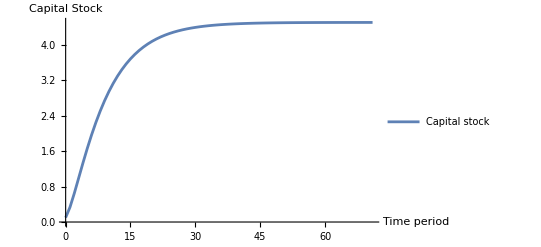

```mathematica
(*Input sample parameters, assuming the model converges to the steady state after T periods*)
α=0.33;
β=0.98;
δ=0.1;
Subscript[k, 0]=0.1;
A=1;
T=70;

(*To solve the model, we attempt to find the values of the state variable (capital) in every period that satisfies all conditions in the competitive equilibrium. The Euler equation, set equal to 0, encompasses all of the necessary conditions for the competitive equilibrium in regard to capital stock. We attempt to solve this equation for all time periods so our equation must be a delayed function of time.*)
eulerEquationDelayed[t_]:=((Subscript[k, t+1]^α)*(A^(1-α))-Subscript[k, t+2]+(1-δ)*(Subscript[k, t+1]))/((Subscript[k, t]^α)*(A^(1-α))-Subscript[k, t+1]+(1-δ)*(Subscript[k, t]))-β(1-δ+α *(A/Subscript[k, t+1])^(1-α))

(*We are told after T periods we are arbitrarily close to the steady state. The values of capital found in the first T-periods (T+1 equations including T=0), are Subscript[K, 0], Subscript[K, 1]... Subscript[K, T], Subscript[K, T+1], Subscript[K, T+2]. As we know Subscript[K, 0], and all values of capital after Subscript[K, T] are at the steady state (Subscript[k, T+2]=Subscript[k, T+1]), therefore we have T+1 equations in T+1 unknowns (Subscript[K, 1]... Subscript[K, T], Subscript[K, ss]).*)

(* We establish the condition Subscript[k, T+2] = Subscript[k, T+1]*)
Subscript[k, T+2]=Subscript[k, T+1];

(*To solve our system of T+1 unknowns and T+1 equations, we use FindRoot (Newton's method). We let our initial guess be 0.2 for each possible value of K, from Subscript[K, 1] to Subscript[K, ss] (excluding Subscript[K, 0] which is given). *)
answerK=FindRoot[

(*We use the 'Table' function to generate a list of T+1 equations indexed for each time period until the steady state. *)
Table[eulerEquationDelayed[t]==0,{t,0,T}],

(*For each of the T+1 unknown values of capital, we use 0.2 as the initial guess*)
Table[{Subscript[k, i],0.2},{i,1,T+1}]];


(*Given our generated solutions are in the format of rules, using 'Table' we can apply these rules to a list of T+1 capital variables, from Subscript[K, 1] to Subscript[K, ss]. This allows for better manipulation*)
capitalShooting=Table[Subscript[k, i],{i,1,Length[answerK]}]/.answerK;

(*To the list of capital values (Subscript[K, 1] to Subscript[K, aa]) we place the value of Subscript[K, 0] at the start. This gives a complete series of capital, up to and including the steady state (Notice we have solved both the firm and household allocations of capital as Subscript[K^f, t] = Subscript[K, t] )*)
capitalShooting=Prepend[capitalShooting,Subscript[k, 0]];

(*Using the first order conditions from our firm problem, we can solve for the wage rate and return on capital*)
wageShooting=(1-α)*(capitalShooting/A)^α A;
returnShooting=α*(A/capitalShooting)^(1-α);

(*Given our previously defined production function and that Subscript[L, t]=Subscript[L^f, t]=1 for all periods, we have an expression for total output in terms of capital and parameters *)
outputShooting=capitalShooting^α A^(1-α);

(*To solve for Investment we need a series of Subscript[K, t+1]. We take Subscript[K, t] and remove Subscript[K, 0] (as Subscript[k, -1] does not exist). Once the steady state is reached capital does not change. The Subscript[K, t+1] series is the Subscript[k, t] series, repeating the last capital value and removing the first*)
capitalP1Shooting=Rest[Append[capitalShooting,Last[capitalShooting]]];

(*By rearranging one of the household problem constraints (the law of capital motion), we can solve for Investment*)
investmentShooting=capitalP1Shooting-(1-δ)capitalShooting;

(*Use the goods market's clearing condition we solve for consumption*)
consumptionShooting=outputShooting-investmentShooting;

(*Given that the percentage of output used for investment is the savings rate, we may also solve for the savings rate as Subscript[I, t]/Subscript[Y, t] = Subscript[s, t]*)
savingShooting= investmentShooting/outputShooting;

(*Plot the evolution of capital stock over time for the best solution.*)
ListPlot[

(*Mathematica indexes lists from 1, but our periods start from T=0. We use 'Table' to subtract 1 from each index,ensuring our graph accurately plots the data.*)
Table[{t,capitalShooting[[t+1]]},{t,0,Length[capitalShooting]-1}],

(*Graph settings, including range, axis labels, and legend*)
Joined->True,PlotRange->All,AxesLabel->{"Time period","Capital Stock"}, PlotLegends->Placed[{"Capital stock"},Below]]
```